# Effet Stark

```mathematica
Clear[]
Off[General::"spell1"]
<<"Units`"
<<"PhysicalConstants`"
$MaxPrecision=150;$MachinePrecision;$MaxExtraPrecision=150;$MaxMachineNumber;
```

### Rb^87 data and other constants

Natural constants

```mathematica
hbar=1.054571596*10^-34; (*Js, ref. Steck*)
Head[hbar];
SetPrecision[hbar,15]; (*to show hbar with 15 numbers*)
Precision[hbar] (*hbar is given in Machine Precision*);
h=hbar*2.*π;
Subscript[μ, 0]=4.*π*10^-7 ; (*N/A^2, exact, ref. Steck*)
c=2.99792458*10^8; (*m/s, exact, ref. Steck*)
Subscript[ϵ, 0]=(Subscript[μ, 0] c^2)^-1; (*F/m, exact, ref. Steck*)
Subscript[k, B]=1.3806503*10^-23 ;(*J/K, ref. Steck*)
Subscript[m, e]=9.10938188*10^-31 (*ElectronMass [kg], ref. Steck*);
Subscript[e, SI]=1.602176462*10^-19 (*ElectronCharge [C], ref. Steck*);
Subscript[e, cgs]=Subscript[e, SI]/(4.π Subscript[ϵ, 0])^(1/2);
Subscript[a, 0]=0.5291772083*10^-10; (*m , Bohr Radius, ref. Steck*)
hbar^2/(Subscript[m, e]*Subscript[e, cgs]^2) (*Subscript[a, 0] calculated*);
Subscript[e, cgs]^2/Subscript[a, 0]/Subscript[e, SI] (*atomic energy unit given in [eV=Subscript[e, SI] V]*)
Subscript[μ, B]=9.27400899*10^-24 ;(*J/T , Bohr Magneton, ref. Steck*)
u=1.66053873*10^-27 ;(*kg, Atomic mass unit , ref. Steck*)
α=Subscript[e, SI]^2/(hbar c 4. π Subscript[ϵ, 0]);
SetPrecision[α,9];
Subscript[R, ∞]=(α^2 Subscript[m, e] c)/(4.π hbar) ;(* Rydberg constant: Wikipedia Subscript[R, ∞]=1.0973731568525(73)*10^7 m^-1, slightly different from value calculated with constants from ref. Steck *) 

SetPrecision[Subscript[R, ∞],13] (*to show Subscript[R, ∞] with 13 numbers*)

(*Rubidium*)

Subscript[m, Rb87]=86.909180520*u; (*kg, Atomic Mass^87 Rb, ref. Steck*)
Subscript[R, Rb87]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb87])^-1 ;(* Subscript[R, Rb]=109736.605 cm^-1 from PRA 67 052502 (2003) Gallagher, "where R_Rb is the Rydberg constant for the reduced electron mass in Rb" -> obviously for Rb85 !! *)
SetPrecision[Subscript[R, Rb87],9] (*to show Subscript[R, ∞] with 9 numbers*)

Subscript[m, Rb85]=84.909180520*u; (*kg, Atomic Mass^85 Rb*)
Subscript[R, Rb85]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb85])^-1 ;
1-(1+Subscript[m, e]/Subscript[m, Rb85])^-1 (*relative effect of reduced mass (replacing Subscript[R, ∞] by Subscript[R, Rb87]) on Energy is in the order of 6E-6*)
Null
```

27.2114

1.09737315688×10^7

1.09736623×10^7

6.46074×10^-6

### Define Functions for calculation of energy-levels without interaction

Quantum defects taken from Publica
tion T. Gallagher et al. PRA 67, 052502 (2003), n>20. nf_j and ng_j states are found in Han, Gallagher et al. PRA 74 054502 (2006)

```mathematica
Subscript[δ, 0]={3.131145,2.65486,2.64165,1.34807,1.34642, 0.0165192,0.0165437,0};
Subscript[δ, 2]={0.195,0.280,0.318,-0.603,-0.545, -0.085,-0.086,0}; (*Meschede values*)

(*Subscript[δ, 0]={3.131804,2.6548849,2.6416737,1.34809171,1.34646572,0.0165192,0.0165437,0}
Subscript[δ, 2]={0.1784,0.2900,0.2950,-0.60286,-0.59600,-0.085,-0.086,0};*)
(*list of quantum defects for Rb85 et Rb87 from PRA 67, 052502 (2003) 1^st entry Subscript[ns, 1/2]: lj=1, 2^nd entry Subscript[np, 1/2]:lj=2,3^nd entry Subscript[np, 3/2]:lj=3, 4^th entry Subscript[nd, 3/2]: lj=4, 5^th entry Subscript[nd, 5/2]:lj=5, 6^th entry Subscript[nf, 5/2]:lj=6, 7^th entry Subscript[nf, 7/2]:lj=7,n>20, 8^th entry for levels with l>f quantum defect is set to zero*)

δ[lj_,n_]:=Subscript[δ, 0][[lj]]+(Subscript[δ, 2][[lj]])/(n-Subscript[δ, 0][[lj]])^2; (*Quantum defect for given lj and n for n>20, see T. Gallagher "Rydberg Atoms"*)
δ[7,41]

(*Energy of Rydberg levels with quantum defect (fine structure)*)

En[lj_,n_]:=-(Subscript[R, Rb87] c)/(n-δ[lj,n])^2 (*[Hz], Energy of Level |n,l,j> with quantum effect and mass correction *)
ERadinte[lj_,n_]:=-(0.5*(1+Subscript[m, e]/Subscript[m, Rb87])^-1)/(n-δ[lj,n])^2 (*[Unit=Atomic Energy Unit = Subscript[e, cgs]^2/Subscript[a, 0] [J] = 2 h Subscript[R, ∞] c [J] = 2*Subscript[E, Hydrogen n=1]], "Energy" as needed by "radinte.exe" of Level |n,l,j> with quantum defect and with reduced mass effect, n>20 *)
(*Effect of mass on Energylevels for Rb^87 and Rb^85*)

Enw85[lj_,n_]:=-(Subscript[R, Rb85] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb85 *)
SetPrecision[(Enw85[1,51]-Enw85[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb85 to control*);
Enw87[lj_,n_]:=-(Subscript[R, Rb87] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb87 *);
SetPrecision[(Enw87[1,51]-Enw87[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb87 to control*);
SetPrecision[(Enw87[1,51]-Enw87[1,50])-(Enw85[1,51]-Enw85[1,50]),15] (* Difference for Transition Frequencies in Hz for Rb87 and Rb85, effect in the order of 10kHz *)
```

0.0164925

7597.31420898438

### Integration of C-Code for Numerov Integration to calculate radial matrix elements, Tests of accuracy by comparison to Hydrogen

Install the external program "radinte.exe" which will be used to calculate the radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration in atomic length unit [a_0^I]   with the following Mathematica syntax: "RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer]".  l1 and l2 are magnetic quantum numbers. E1 and E2 are the Energies of the levels |n,l,j> calculated with quantum defect and with mass correction in atomic energy units ([e_cgs)^2/a_0] done by ERadinte[lj_,n_].
Attention: The Real numbers E1 and E2 have to be in floating point representation, otherwise Mathlink (communication between radinte.exe and Mathematica) will hang up!! The calculation in radinte.exe is done in double precision.

```mathematica
Install["D:\\Doktorarbeit\\Simus\\Mathematica\\radinte\\radinte\\Debug\\radinte.exe"]
?RadIntE

(*Test: Comparison with existing .exe file *)
RadIntE[
  ERadinte[1,50],-0.0453211,0,1,1]
RadIntE[-0.0453211,ERadinte[1,50],1,0,1]
RadIntE[-0.03661927,ERadinte[1,50],1,0,1]
Timing[RadIntE[-0.03661928,-0.0002276161,1,0,1]]
```

LinkObject["D:\Documents\raulcteixeira\Documents\Simulations et calculs\Simulation_Rydberg + taille du BEC dans piège magnétique\Spectres VdW\radinte\radinte.exe",35,9]

RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer] calculates radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration.

-0.0267757

-0.0267757

0.00739872

{0.,0.00741686}

## | 58 s1/2 >

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=30;Subscript[l, 1]=0;Subscript[j, 1]=1/2;Subscript[m, 1]=1/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=20; Subscript[n, max]=40;

δf=1000*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤i-1,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,If[Subscript[m, A]==Subscript[m, 1],t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]]
]]
]
Length[NList]

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
NList
```

-4.55704×10^12

{0.078,Null}

326

{{25,3,5/2,1/2,-5.27062×10^12,-1},{25,3,7/2,1/2,-5.27063×10^12,-1},{25,4,7/2,1/2,-5.26371×10^12,1},{25,4,9/2,1/2,-5.26371×10^12,1},{25,5,9/2,1/2,-5.26371×10^12,-1},{25,5,11/2,1/2,-5.26371×10^12,-1},{25,6,11/2,1/2,-5.26371×10^12,1},{25,6,13/2,1/2,-5.26371×10^12,1},{25,7,13/2,1/2,-5.26371×10^12,-1},{25,7,15/2,1/2,-5.26371×10^12,-1},{25,8,15/2,1/2,-5.26371×10^12,1},{25,8,17/2,1/2,-5.26371×10^12,1},{25,9,17/2,1/2,-5.26371×10^12,-1},{25,9,19/2,1/2,-5.26371×10^12,-1},{25,10,19/2,1/2,-5.26371×10^12,1},{25,10,21/2,1/2,-5.26371×10^12,1},{25,11,21/2,1/2,-5.26371×10^12,-1},{25,11,23/2,1/2,-5.26371×10^12,-1},{25,12,23/2,1/2,-5.26371×10^12,1},{25,12,25/2,1/2,-5.26371×10^12,1},{25,13,25/2,1/2,-5.26371×10^12,-1},{25,13,27/2,1/2,-5.26371×10^12,-1},{25,14,27/2,1/2,-5.26371×10^12,1},{25,14,29/2,1/2,-5.26371×10^12,1},{25,15,29/2,1/2,-5.26371×10^12,-1},{25,15,31/2,1/2,-5.26371×10^12,-1},{25,16,31/2,1/2,-5.26371×10^12,1},{25,16,33/2,1/2,-5.26371×10^12,1},{25,17,33/2,1/2,-5.26371×10^12,-1},{25,17,35/2,1/2,-5.26371×10^12,-1},{25,18,35/2,1/2,-5.26371×10^12,1},{25,18,37/2,1/2,-5.26371×10^12,1},{25,19,37/2,1/2,-5.26371×10^12,-1},{25,19,39/2,1/2,-5.26371×10^12,-1},{25,20,39/2,1/2,-5.26371×10^12,1},{25,20,41/2,1/2,-5.26371×10^12,1},{25,21,41/2,1/2,-5.26371×10^12,-1},{25,21,43/2,1/2,-5.26371×10^12,-1},{25,22,43/2,1/2,-5.26371×10^12,1},{25,22,45/2,1/2,-5.26371×10^12,1},{25,23,45/2,1/2,-5.26371×10^12,-1},{25,23,47/2,1/2,-5.26371×10^12,-1},{25,24,47/2,1/2,-5.26371×10^12,1},{25,24,49/2,1/2,-5.26371×10^12,1},{26,2,3/2,1/2,-5.41297×10^12,1},{26,2,5/2,1/2,-5.41229×10^12,1},{26,3,5/2,1/2,-4.87274×10^12,-1},{26,3,7/2,1/2,-4.87275×10^12,-1},{26,4,7/2,1/2,-4.8666×10^12,1},{26,4,9/2,1/2,-4.8666×10^12,1},{26,5,9/2,1/2,-4.8666×10^12,-1},{26,5,11/2,1/2,-4.8666×10^12,-1},{26,6,11/2,1/2,-4.8666×10^12,1},{26,6,13/2,1/2,-4.8666×10^12,1},{26,7,13/2,1/2,-4.8666×10^12,-1},{26,7,15/2,1/2,-4.8666×10^12,-1},{26,8,15/2,1/2,-4.8666×10^12,1},{26,8,17/2,1/2,-4.8666×10^12,1},{26,9,17/2,1/2,-4.8666×10^12,-1},{26,9,19/2,1/2,-4.8666×10^12,-1},{26,10,19/2,1/2,-4.8666×10^12,1},{26,10,21/2,1/2,-4.8666×10^12,1},{26,11,21/2,1/2,-4.8666×10^12,-1},{26,11,23/2,1/2,-4.8666×10^12,-1},{26,12,23/2,1/2,-4.8666×10^12,1},{26,12,25/2,1/2,-4.8666×10^12,1},{26,13,25/2,1/2,-4.8666×10^12,-1},{26,13,27/2,1/2,-4.8666×10^12,-1},{26,14,27/2,1/2,-4.8666×10^12,1},{26,14,29/2,1/2,-4.8666×10^12,1},{26,15,29/2,1/2,-4.8666×10^12,-1},{26,15,31/2,1/2,-4.8666×10^12,-1},{26,16,31/2,1/2,-4.8666×10^12,1},{26,16,33/2,1/2,-4.8666×10^12,1},{26,17,33/2,1/2,-4.8666×10^12,-1},{26,17,35/2,1/2,-4.8666×10^12,-1},{26,18,35/2,1/2,-4.8666×10^12,1},{26,18,37/2,1/2,-4.8666×10^12,1},{26,19,37/2,1/2,-4.8666×10^12,-1},{26,19,39/2,1/2,-4.8666×10^12,-1},{26,20,39/2,1/2,-4.8666×10^12,1},{26,20,41/2,1/2,-4.8666×10^12,1},{26,21,41/2,1/2,-4.8666×10^12,-1},{26,21,43/2,1/2,-4.8666×10^12,-1},{26,22,43/2,1/2,-4.8666×10^12,1},{26,22,45/2,1/2,-4.8666×10^12,1},{26,23,45/2,1/2,-4.8666×10^12,-1},{26,23,47/2,1/2,-4.8666×10^12,-1},{26,24,47/2,1/2,-4.8666×10^12,1},{26,24,49/2,1/2,-4.8666×10^12,1},{26,25,49/2,1/2,-4.8666×10^12,-1},{26,25,51/2,1/2,-4.8666×10^12,-1},{27,1,1/2,1/2,-5.55092×10^12,-1},{27,1,3/2,1/2,-5.54492×10^12,-1},{27,2,3/2,1/2,-4.99921×10^12,1},{27,2,5/2,1/2,-4.9986×10^12,1},{27,3,5/2,1/2,-4.51827×10^12,-1},{27,3,7/2,1/2,-4.51828×10^12,-1},{27,4,7/2,1/2,-4.51279×10^12,1},{27,4,9/2,1/2,-4.51279×10^12,1},{27,5,9/2,1/2,-4.51279×10^12,-1},{27,5,11/2,1/2,-4.51279×10^12,-1},{27,6,11/2,1/2,-4.51279×10^12,1},{27,6,13/2,1/2,-4.51279×10^12,1},{27,7,13/2,1/2,-4.51279×10^12,-1},{27,7,15/2,1/2,-4.51279×10^12,-1},{27,8,15/2,1/2,-4.51279×10^12,1},{27,8,17/2,1/2,-4.51279×10^12,1},{27,9,17/2,1/2,-4.51279×10^12,-1},{27,9,19/2,1/2,-4.51279×10^12,-1},{27,10,19/2,1/2,-4.51279×10^12,1},{27,10,21/2,1/2,-4.51279×10^12,1},{27,11,21/2,1/2,-4.51279×10^12,-1},{27,11,23/2,1/2,-4.51279×10^12,-1},{27,12,23/2,1/2,-4.51279×10^12,1},{27,12,25/2,1/2,-4.51279×10^12,1},{27,13,25/2,1/2,-4.51279×10^12,-1},{27,13,27/2,1/2,-4.51279×10^12,-1},{27,14,27/2,1/2,-4.51279×10^12,1},{27,14,29/2,1/2,-4.51279×10^12,1},{27,15,29/2,1/2,-4.51279×10^12,-1},{27,15,31/2,1/2,-4.51279×10^12,-1},{27,16,31/2,1/2,-4.51279×10^12,1},{27,16,33/2,1/2,-4.51279×10^12,1},{27,17,33/2,1/2,-4.51279×10^12,-1},{27,17,35/2,1/2,-4.51279×10^12,-1},{27,18,35/2,1/2,-4.51279×10^12,1},{27,18,37/2,1/2,-4.51279×10^12,1},{27,19,37/2,1/2,-4.51279×10^12,-1},{27,19,39/2,1/2,-4.51279×10^12,-1},{27,20,39/2,1/2,-4.51279×10^12,1},{27,20,41/2,1/2,-4.51279×10^12,1},{27,21,41/2,1/2,-4.51279×10^12,-1},{27,21,43/2,1/2,-4.51279×10^12,-1},{27,22,43/2,1/2,-4.51279×10^12,1},{27,22,45/2,1/2,-4.51279×10^12,1},{27,23,45/2,1/2,-4.51279×10^12,-1},{27,23,47/2,1/2,-4.51279×10^12,-1},{27,24,47/2,1/2,-4.51279×10^12,1},{27,24,49/2,1/2,-4.51279×10^12,1},{27,25,49/2,1/2,-4.51279×10^12,-1},{27,25,51/2,1/2,-4.51279×10^12,-1},{27,26,51/2,1/2,-4.51279×10^12,1},{27,26,53/2,1/2,-4.51279×10^12,1},{28,0,1/2,1/2,-5.31951×10^12,1},{28,1,1/2,1/2,-5.12151×10^12,-1},{28,1,3/2,1/2,-5.1162×10^12,-1},{28,2,3/2,1/2,-4.63113×10^12,1},{28,2,5/2,1/2,-4.63059×10^12,1},{28,3,5/2,1/2,-4.20112×10^12,-1},{28,3,7/2,1/2,-4.20113×10^12,-1},{28,4,7/2,1/2,-4.1962×10^12,1},{28,4,9/2,1/2,-4.1962×10^12,1},{28,5,9/2,1/2,-4.1962×10^12,-1},{28,5,11/2,1/2,-4.1962×10^12,-1},{28,6,11/2,1/2,-4.1962×10^12,1},{28,6,13/2,1/2,-4.1962×10^12,1},{28,7,13/2,1/2,-4.1962×10^12,-1},{28,7,15/2,1/2,-4.1962×10^12,-1},{28,8,15/2,1/2,-4.1962×10^12,1},{28,8,17/2,1/2,-4.1962×10^12,1},{28,9,17/2,1/2,-4.1962×10^12,-1},{28,9,19/2,1/2,-4.1962×10^12,-1},{28,10,19/2,1/2,-4.1962×10^12,1},{28,10,21/2,1/2,-4.1962×10^12,1},{28,11,21/2,1/2,-4.1962×10^12,-1},{28,11,23/2,1/2,-4.1962×10^12,-1},{28,12,23/2,1/2,-4.1962×10^12,1},{28,12,25/2,1/2,-4.1962×10^12,1},{28,13,25/2,1/2,-4.1962×10^12,-1},{28,13,27/2,1/2,-4.1962×10^12,-1},{28,14,27/2,1/2,-4.1962×10^12,1},{28,14,29/2,1/2,-4.1962×10^12,1},{28,15,29/2,1/2,-4.1962×10^12,-1},{28,15,31/2,1/2,-4.1962×10^12,-1},{28,16,31/2,1/2,-4.1962×10^12,1},{28,16,33/2,1/2,-4.1962×10^12,1},{28,17,33/2,1/2,-4.1962×10^12,-1},{28,17,35/2,1/2,-4.1962×10^12,-1},{28,18,35/2,1/2,-4.1962×10^12,1},{28,18,37/2,1/2,-4.1962×10^12,1},{28,19,37/2,1/2,-4.1962×10^12,-1},{28,19,39/2,1/2,-4.1962×10^12,-1},{28,20,39/2,1/2,-4.1962×10^12,1},{28,20,41/2,1/2,-4.1962×10^12,1},{28,21,41/2,1/2,-4.1962×10^12,-1},{28,21,43/2,1/2,-4.1962×10^12,-1},{28,22,43/2,1/2,-4.1962×10^12,1},{28,22,45/2,1/2,-4.1962×10^12,1},{28,23,45/2,1/2,-4.1962×10^12,-1},{28,23,47/2,1/2,-4.1962×10^12,-1},{28,24,47/2,1/2,-4.1962×10^12,1},{28,24,49/2,1/2,-4.1962×10^12,1},{28,25,49/2,1/2,-4.1962×10^12,-1},{28,25,51/2,1/2,-4.1962×10^12,-1},{28,26,51/2,1/2,-4.1962×10^12,1},{28,26,53/2,1/2,-4.1962×10^12,1},{28,27,53/2,1/2,-4.1962×10^12,-1},{28,27,55/2,1/2,-4.1962×10^12,-1},{29,0,1/2,1/2,-4.91618×10^12,1},{29,1,1/2,1/2,-4.74007×10^12,-1},{29,1,3/2,1/2,-4.73534×10^12,-1},{29,2,3/2,1/2,-4.30226×10^12,1},{29,2,5/2,1/2,-4.30177×10^12,1},{29,3,5/2,1/2,-3.91623×10^12,-1},{29,3,7/2,1/2,-3.91624×10^12,-1},{29,4,7/2,1/2,-3.9118×10^12,1},{29,4,9/2,1/2,-3.9118×10^12,1},{29,5,9/2,1/2,-3.9118×10^12,-1},{29,5,11/2,1/2,-3.9118×10^12,-1},{29,6,11/2,1/2,-3.9118×10^12,1},{29,6,13/2,1/2,-3.9118×10^12,1},{29,7,13/2,1/2,-3.9118×10^12,-1},{29,7,15/2,1/2,-3.9118×10^12,-1},{29,8,15/2,1/2,-3.9118×10^12,1},{29,8,17/2,1/2,-3.9118×10^12,1},{29,9,17/2,1/2,-3.9118×10^12,-1},{29,9,19/2,1/2,-3.9118×10^12,-1},{29,10,19/2,1/2,-3.9118×10^12,1},{29,10,21/2,1/2,-3.9118×10^12,1},{29,11,21/2,1/2,-3.9118×10^12,-1},{29,11,23/2,1/2,-3.9118×10^12,-1},{29,12,23/2,1/2,-3.9118×10^12,1},{29,12,25/2,1/2,-3.9118×10^12,1},{29,13,25/2,1/2,-3.9118×10^12,-1},{29,13,27/2,1/2,-3.9118×10^12,-1},{29,14,27/2,1/2,-3.9118×10^12,1},{29,14,29/2,1/2,-3.9118×10^12,1},{29,15,29/2,1/2,-3.9118×10^12,-1},{29,15,31/2,1/2,-3.9118×10^12,-1},{29,16,31/2,1/2,-3.9118×10^12,1},{29,16,33/2,1/2,-3.9118×10^12,1},{29,17,33/2,1/2,-3.9118×10^12,-1},{29,17,35/2,1/2,-3.9118×10^12,-1},{29,18,35/2,1/2,-3.9118×10^12,1},{29,18,37/2,1/2,-3.9118×10^12,1},{29,19,37/2,1/2,-3.9118×10^12,-1},{29,19,39/2,1/2,-3.9118×10^12,-1},{29,20,39/2,1/2,-3.9118×10^12,1},{29,20,41/2,1/2,-3.9118×10^12,1},{29,21,41/2,1/2,-3.9118×10^12,-1},{29,21,43/2,1/2,-3.9118×10^12,-1},{29,22,43/2,1/2,-3.9118×10^12,1},{29,22,45/2,1/2,-3.9118×10^12,1},{29,23,45/2,1/2,-3.9118×10^12,-1},{29,23,47/2,1/2,-3.9118×10^12,-1},{29,24,47/2,1/2,-3.9118×10^12,1},{29,24,49/2,1/2,-3.9118×10^12,1},{29,25,49/2,1/2,-3.9118×10^12,-1},{29,25,51/2,1/2,-3.9118×10^12,-1},{29,26,51/2,1/2,-3.9118×10^12,1},{29,26,53/2,1/2,-3.9118×10^12,1},{29,27,53/2,1/2,-3.9118×10^12,-1},{29,27,55/2,1/2,-3.9118×10^12,-1},{29,28,55/2,1/2,-3.9118×10^12,1},{29,28,57/2,1/2,-3.9118×10^12,1},{30,0,1/2,1/2,-4.55704×10^12,1},{30,1,1/2,1/2,-4.39971×10^12,-1},{30,1,3/2,1/2,-4.39548×10^12,-1},{30,2,3/2,1/2,-4.00721×10^12,1},{30,2,5/2,1/2,-4.00677×10^12,1},{30,3,5/2,1/2,-3.65936×10^12,-1},{30,3,7/2,1/2,-3.65937×10^12,-1},{30,4,7/2,1/2,-3.65536×10^12,1},{30,4,9/2,1/2,-3.65536×10^12,1},{30,5,9/2,1/2,-3.65536×10^12,-1},{30,5,11/2,1/2,-3.65536×10^12,-1},{30,6,11/2,1/2,-3.65536×10^12,1},{30,6,13/2,1/2,-3.65536×10^12,1},{30,7,13/2,1/2,-3.65536×10^12,-1},{30,7,15/2,1/2,-3.65536×10^12,-1},{30,8,15/2,1/2,-3.65536×10^12,1},{30,8,17/2,1/2,-3.65536×10^12,1},{30,9,17/2,1/2,-3.65536×10^12,-1},{30,9,19/2,1/2,-3.65536×10^12,-1},{30,10,19/2,1/2,-3.65536×10^12,1},{30,10,21/2,1/2,-3.65536×10^12,1},{30,11,21/2,1/2,-3.65536×10^12,-1},{30,11,23/2,1/2,-3.65536×10^12,-1},{30,12,23/2,1/2,-3.65536×10^12,1},{30,12,25/2,1/2,-3.65536×10^12,1},{30,13,25/2,1/2,-3.65536×10^12,-1},{30,13,27/2,1/2,-3.65536×10^12,-1},{30,14,27/2,1/2,-3.65536×10^12,1},{30,14,29/2,1/2,-3.65536×10^12,1},{30,15,29/2,1/2,-3.65536×10^12,-1},{30,15,31/2,1/2,-3.65536×10^12,-1},{30,16,31/2,1/2,-3.65536×10^12,1},{30,16,33/2,1/2,-3.65536×10^12,1},{30,17,33/2,1/2,-3.65536×10^12,-1},{30,17,35/2,1/2,-3.65536×10^12,-1},{30,18,35/2,1/2,-3.65536×10^12,1},{30,18,37/2,1/2,-3.65536×10^12,1},{30,19,37/2,1/2,-3.65536×10^12,-1},{30,19,39/2,1/2,-3.65536×10^12,-1},{30,20,39/2,1/2,-3.65536×10^12,1},{30,20,41/2,1/2,-3.65536×10^12,1},{30,21,41/2,1/2,-3.65536×10^12,-1},{30,21,43/2,1/2,-3.65536×10^12,-1},{30,22,43/2,1/2,-3.65536×10^12,1},{30,22,45/2,1/2,-3.65536×10^12,1},{30,23,45/2,1/2,-3.65536×10^12,-1},{30,23,47/2,1/2,-3.65536×10^12,-1},{30,24,47/2,1/2,-3.65536×10^12,1},{30,24,49/2,1/2,-3.65536×10^12,1},{30,25,49/2,1/2,-3.65536×10^12,-1},{30,25,51/2,1/2,-3.65536×10^12,-1},{30,26,51/2,1/2,-3.65536×10^12,1},{30,26,53/2,1/2,-3.65536×10^12,1},{30,27,53/2,1/2,-3.65536×10^12,-1},{30,27,55/2,1/2,-3.65536×10^12,-1},{30,28,55/2,1/2,-3.65536×10^12,1},{30,28,57/2,1/2,-3.65536×10^12,1},{30,29,57/2,1/2,-3.65536×10^12,-1},{30,29,59/2,1/2,-3.65536×10^12,-1},{31,0,1/2,1/2,-4.23586×10^12,1},{31,1,1/2,1/2,-4.09473×10^12,-1},{31,1,3/2,1/2,-4.09093×10^12,-1},{31,2,3/2,1/2,-3.7415×10^12,1},{31,2,5/2,1/2,-3.7411×10^12,1},{32,0,1/2,1/2,-3.94748×10^12,1},{32,1,1/2,1/2,-3.82041×10^12,-1},{32,1,3/2,1/2,-3.81698×10^12,-1},{33,0,1/2,1/2,-3.68758×10^12,1},{33,1,1/2,1/2,-3.57275×10^12,-1},{33,1,3/2,1/2,-3.56965×10^12,-1}}

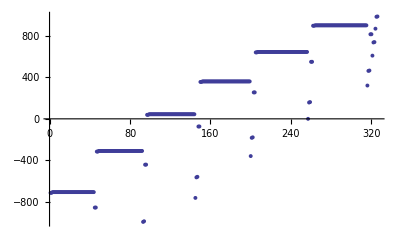

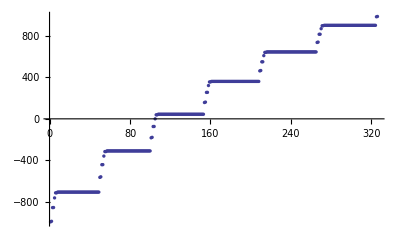

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

```mathematica
Calcul des éléments de matrice non-diagonaux
```

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]

(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);



EMatrixelement[{60,0,1/2,1/2},{58,1,1/2,-1/2}]


(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]
```

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{160.499,0.-160.499 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, 1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, 1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

{28.533,Null}

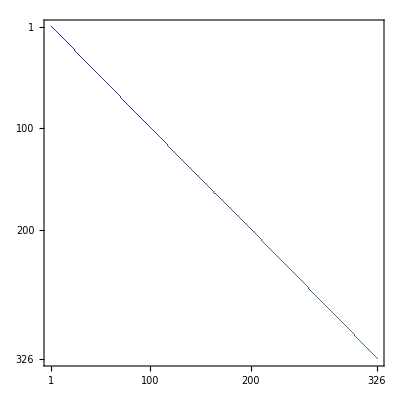

```mathematica
(*Absolute Energies of disturbed levels:*)

Clear[i,f,R]
EI={};
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ] ;
EIList = {} ;
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
MatrixPlot[EI]
```

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=301;
ELabel=300;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList;
```

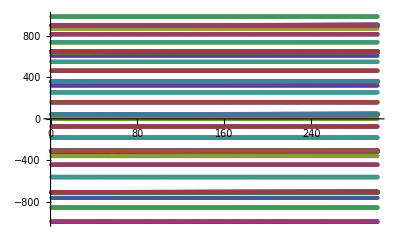

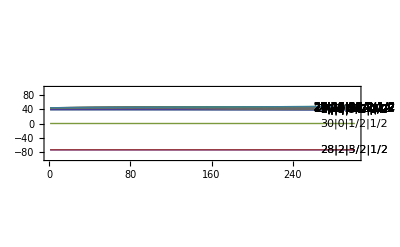

```mathematica
ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

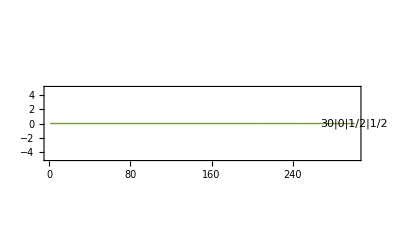

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-5,5}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

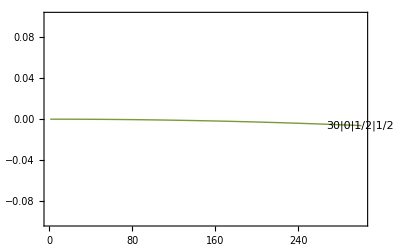

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-0.1,0.1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

```mathematica
LabelList[[105]]
LabelList
```

30|0|1/2|1/2

{27|1|1/2|1/2,27|1|3/2|1/2,26|2|3/2|1/2,26|2|5/2|1/2,28|0|1/2|1/2,25|3|7/2|1/2,25|3|5/2|1/2,25|4|7/2|1/2,25|4|9/2|1/2,25|5|9/2|1/2,25|5|11/2|1/2,25|6|11/2|1/2,25|6|13/2|1/2,25|7|13/2|1/2,25|7|15/2|1/2,25|8|15/2|1/2,25|8|17/2|1/2,25|9|17/2|1/2,25|9|19/2|1/2,25|10|19/2|1/2,25|10|21/2|1/2,25|11|21/2|1/2,25|11|23/2|1/2,25|12|23/2|1/2,25|12|25/2|1/2,25|13|25/2|1/2,25|13|27/2|1/2,25|14|27/2|1/2,25|14|29/2|1/2,25|15|29/2|1/2,25|15|31/2|1/2,25|16|31/2|1/2,25|16|33/2|1/2,25|17|33/2|1/2,25|17|35/2|1/2,25|18|35/2|1/2,25|18|37/2|1/2,25|19|37/2|1/2,25|19|39/2|1/2,25|20|39/2|1/2,25|20|41/2|1/2,25|21|41/2|1/2,25|21|43/2|1/2,25|22|43/2|1/2,25|22|45/2|1/2,25|23|45/2|1/2,25|23|47/2|1/2,25|24|47/2|1/2,25|24|49/2|1/2,28|1|1/2|1/2,28|1|3/2|1/2,27|2|3/2|1/2,27|2|5/2|1/2,29|0|1/2|1/2,26|3|7/2|1/2,26|3|5/2|1/2,26|4|7/2|1/2,26|4|9/2|1/2,26|5|9/2|1/2,26|5|11/2|1/2,26|6|11/2|1/2,26|6|13/2|1/2,26|7|13/2|1/2,26|7|15/2|1/2,26|8|15/2|1/2,26|8|17/2|1/2,26|9|17/2|1/2,26|9|19/2|1/2,26|10|19/2|1/2,26|10|21/2|1/2,26|11|21/2|1/2,26|11|23/2|1/2,26|12|23/2|1/2,26|12|25/2|1/2,26|13|25/2|1/2,26|13|27/2|1/2,26|14|27/2|1/2,26|14|29/2|1/2,26|15|29/2|1/2,26|15|31/2|1/2,26|16|31/2|1/2,26|16|33/2|1/2,26|17|33/2|1/2,26|17|35/2|1/2,26|18|35/2|1/2,26|18|37/2|1/2,26|19|37/2|1/2,26|19|39/2|1/2,26|20|39/2|1/2,26|20|41/2|1/2,26|21|41/2|1/2,26|21|43/2|1/2,26|22|43/2|1/2,26|22|45/2|1/2,26|23|45/2|1/2,26|23|47/2|1/2,26|24|47/2|1/2,26|24|49/2|1/2,26|25|49/2|1/2,26|25|51/2|1/2,29|1|1/2|1/2,29|1|3/2|1/2,28|2|3/2|1/2,28|2|5/2|1/2,30|0|1/2|1/2,27|3|7/2|1/2,27|3|5/2|1/2,27|4|7/2|1/2,27|4|9/2|1/2,27|5|9/2|1/2,27|5|11/2|1/2,27|6|11/2|1/2,27|6|13/2|1/2,27|7|13/2|1/2,27|7|15/2|1/2,27|8|15/2|1/2,27|8|17/2|1/2,27|9|17/2|1/2,27|9|19/2|1/2,27|10|19/2|1/2,27|10|21/2|1/2,27|11|21/2|1/2,27|11|23/2|1/2,27|12|23/2|1/2,27|12|25/2|1/2,27|13|25/2|1/2,27|13|27/2|1/2,27|14|27/2|1/2,27|14|29/2|1/2,27|15|29/2|1/2,27|15|31/2|1/2,27|16|31/2|1/2,27|16|33/2|1/2,27|17|33/2|1/2,27|17|35/2|1/2,27|18|35/2|1/2,27|18|37/2|1/2,27|19|37/2|1/2,27|19|39/2|1/2,27|20|39/2|1/2,27|20|41/2|1/2,27|21|41/2|1/2,27|21|43/2|1/2,27|22|43/2|1/2,27|22|45/2|1/2,27|23|45/2|1/2,27|23|47/2|1/2,27|24|47/2|1/2,27|24|49/2|1/2,27|25|49/2|1/2,27|25|51/2|1/2,27|26|51/2|1/2,27|26|53/2|1/2,30|1|1/2|1/2,30|1|3/2|1/2,29|2|3/2|1/2,29|2|5/2|1/2,31|0|1/2|1/2,28|3|7/2|1/2,28|3|5/2|1/2,28|4|7/2|1/2,28|4|9/2|1/2,28|5|9/2|1/2,28|5|11/2|1/2,28|6|11/2|1/2,28|6|13/2|1/2,28|7|13/2|1/2,28|7|15/2|1/2,28|8|15/2|1/2,28|8|17/2|1/2,28|9|17/2|1/2,28|9|19/2|1/2,28|10|19/2|1/2,28|10|21/2|1/2,28|11|21/2|1/2,28|11|23/2|1/2,28|12|23/2|1/2,28|12|25/2|1/2,28|13|25/2|1/2,28|13|27/2|1/2,28|14|27/2|1/2,28|14|29/2|1/2,28|15|29/2|1/2,28|15|31/2|1/2,28|16|31/2|1/2,28|16|33/2|1/2,28|17|33/2|1/2,28|17|35/2|1/2,28|18|35/2|1/2,28|18|37/2|1/2,28|19|37/2|1/2,28|19|39/2|1/2,28|20|39/2|1/2,28|20|41/2|1/2,28|21|41/2|1/2,28|21|43/2|1/2,28|22|43/2|1/2,28|22|45/2|1/2,28|23|45/2|1/2,28|23|47/2|1/2,28|24|47/2|1/2,28|24|49/2|1/2,28|25|49/2|1/2,28|25|51/2|1/2,28|26|51/2|1/2,28|26|53/2|1/2,28|27|53/2|1/2,28|27|55/2|1/2,31|1|1/2|1/2,31|1|3/2|1/2,30|2|3/2|1/2,30|2|5/2|1/2,32|0|1/2|1/2,29|3|7/2|1/2,29|3|5/2|1/2,29|4|7/2|1/2,29|4|9/2|1/2,29|5|9/2|1/2,29|5|11/2|1/2,29|6|11/2|1/2,29|6|13/2|1/2,29|7|13/2|1/2,29|7|15/2|1/2,29|8|15/2|1/2,29|8|17/2|1/2,29|9|17/2|1/2,29|9|19/2|1/2,29|10|19/2|1/2,29|10|21/2|1/2,29|11|21/2|1/2,29|11|23/2|1/2,29|12|23/2|1/2,29|12|25/2|1/2,29|13|25/2|1/2,29|13|27/2|1/2,29|14|27/2|1/2,29|14|29/2|1/2,29|15|29/2|1/2,29|15|31/2|1/2,29|16|31/2|1/2,29|16|33/2|1/2,29|17|33/2|1/2,29|17|35/2|1/2,29|18|35/2|1/2,29|18|37/2|1/2,29|19|37/2|1/2,29|19|39/2|1/2,29|20|39/2|1/2,29|20|41/2|1/2,29|21|41/2|1/2,29|21|43/2|1/2,29|22|43/2|1/2,29|22|45/2|1/2,29|23|45/2|1/2,29|23|47/2|1/2,29|24|47/2|1/2,29|24|49/2|1/2,29|25|49/2|1/2,29|25|51/2|1/2,29|26|51/2|1/2,29|26|53/2|1/2,29|27|53/2|1/2,29|27|55/2|1/2,29|28|55/2|1/2,29|28|57/2|1/2,32|1|1/2|1/2,32|1|3/2|1/2,31|2|3/2|1/2,31|2|5/2|1/2,33|0|1/2|1/2,30|3|7/2|1/2,30|3|5/2|1/2,30|4|7/2|1/2,30|4|9/2|1/2,30|5|9/2|1/2,30|5|11/2|1/2,30|6|11/2|1/2,30|6|13/2|1/2,30|7|13/2|1/2,30|7|15/2|1/2,30|8|15/2|1/2,30|8|17/2|1/2,30|9|17/2|1/2,30|9|19/2|1/2,30|10|19/2|1/2,30|10|21/2|1/2,30|11|21/2|1/2,30|11|23/2|1/2,30|12|23/2|1/2,30|12|25/2|1/2,30|13|25/2|1/2,30|13|27/2|1/2,30|14|27/2|1/2,30|14|29/2|1/2,30|15|29/2|1/2,30|15|31/2|1/2,30|16|31/2|1/2,30|16|33/2|1/2,30|17|33/2|1/2,30|17|35/2|1/2,30|18|35/2|1/2,30|18|37/2|1/2,30|19|37/2|1/2,30|19|39/2|1/2,30|20|39/2|1/2,30|20|41/2|1/2,30|21|41/2|1/2,30|21|43/2|1/2,30|22|43/2|1/2,30|22|45/2|1/2,30|23|45/2|1/2,30|23|47/2|1/2,30|24|47/2|1/2,30|24|49/2|1/2,30|25|49/2|1/2,30|25|51/2|1/2,30|26|51/2|1/2,30|26|53/2|1/2,30|27|53/2|1/2,30|27|55/2|1/2,30|28|55/2|1/2,30|28|57/2|1/2,30|29|57/2|1/2,30|29|59/2|1/2,33|1|1/2|1/2,33|1|3/2|1/2}

```mathematica
}
```

```mathematica
MPList[[105]]

Export["30s_stark_Shift.dat",MPList[[105]]]
```

{{1,-6.89943×10^-8},{2,-2.75954×10^-7},{3,-6.20919×10^-7},{4,-1.10384×10^-6},{5,-1.72476×10^-6},{6,-2.48366×10^-6},{7,-3.38054×10^-6},{8,-4.41539×10^-6},{9,-5.58823×10^-6},{10,-6.89905×10^-6},{11,-8.34786×10^-6},{12,-9.93464×10^-6},{13,-0.0000116594},{14,-0.0000135221},{15,-0.0000155229},{16,-0.0000176616},{17,-0.0000199383},{18,-0.0000223529},{19,-0.0000249056},{20,-0.0000275962},{21,-0.0000304248},{22,-0.0000333914},{23,-0.000036496},{24,-0.0000397386},{25,-0.0000431191},{26,-0.0000466376},{27,-0.0000502941},{28,-0.0000540886},{29,-0.0000580211},{30,-0.0000620915},{31,-0.0000663},{32,-0.0000706464},{33,-0.0000751308},{34,-0.0000797532},{35,-0.0000845135},{36,-0.0000894119},{37,-0.0000944482},{38,-0.0000996225},{39,-0.000104935},{40,-0.000110385},{41,-0.000115973},{42,-0.0001217},{43,-0.000127564},{44,-0.000133566},{45,-0.000139706},{46,-0.000145984},{47,-0.000152401},{48,-0.000158955},{49,-0.000165647},{50,-0.000172477},{51,-0.000179445},{52,-0.000186551},{53,-0.000193795},{54,-0.000201177},{55,-0.000208697},{56,-0.000216355},{57,-0.000224151},{58,-0.000232085},{59,-0.000240157},{60,-0.000248367},{61,-0.000256715},{62,-0.000265201},{63,-0.000273825},{64,-0.000282587},{65,-0.000291487},{66,-0.000300524},{67,-0.0003097},{68,-0.000319014},{69,-0.000328466},{70,-0.000338056},{71,-0.000347784},{72,-0.000357649},{73,-0.000367653},{74,-0.000377795},{75,-0.000388075},{76,-0.000398492},{77,-0.000409048},{78,-0.000419742},{79,-0.000430574},{80,-0.000441543},{81,-0.000452651},{82,-0.000463897},{83,-0.00047528},{84,-0.000486802},{85,-0.000498461},{86,-0.000510259},{87,-0.000522195},{88,-0.000534268},{89,-0.00054648},{90,-0.000558829},{91,-0.000571317},{92,-0.000583943},{93,-0.000596706},{94,-0.000609608},{95,-0.000622647},{96,-0.000635825},{97,-0.00064914},{98,-0.000662594},{99,-0.000676185},{100,-0.000689915},{101,-0.000703782},{102,-0.000717788},{103,-0.000731931},{104,-0.000746213},{105,-0.000760632},{106,-0.00077519},{107,-0.000789885},{108,-0.000804719},{109,-0.00081969},{110,-0.000834799},{111,-0.000850047},{112,-0.000865432},{113,-0.000880956},{114,-0.000896617},{115,-0.000912417},{116,-0.000928354},{117,-0.000944429},{118,-0.000960643},{119,-0.000976994},{120,-0.000993484},{121,-0.00101011},{122,-0.00102688},{123,-0.00104378},{124,-0.00106082},{125,-0.001078},{126,-0.00109532},{127,-0.00111277},{128,-0.00113037},{129,-0.0011481},{130,-0.00116597},{131,-0.00118397},{132,-0.00120212},{133,-0.0012204},{134,-0.00123882},{135,-0.00125738},{136,-0.00127608},{137,-0.00129492},{138,-0.00131389},{139,-0.001333},{140,-0.00135225},{141,-0.00137164},{142,-0.00139116},{143,-0.00141083},{144,-0.00143063},{145,-0.00145057},{146,-0.00147065},{147,-0.00149086},{148,-0.00151121},{149,-0.00153171},{150,-0.00155234},{151,-0.0015731},{152,-0.00159401},{153,-0.00161505},{154,-0.00163623},{155,-0.00165755},{156,-0.00167901},{157,-0.00170061},{158,-0.00172234},{159,-0.00174421},{160,-0.00176622},{161,-0.00178837},{162,-0.00181065},{163,-0.00183308},{164,-0.00185564},{165,-0.00187834},{166,-0.00190118},{167,-0.00192415},{168,-0.00194727},{169,-0.00197052},{170,-0.00199391},{171,-0.00201743},{172,-0.0020411},{173,-0.0020649},{174,-0.00208885},{175,-0.00211293},{176,-0.00213714},{177,-0.0021615},{178,-0.00218599},{179,-0.00221063},{180,-0.00223539},{181,-0.0022603},{182,-0.00228535},{183,-0.00231053},{184,-0.00233585},{185,-0.00236131},{186,-0.00238691},{187,-0.00241265},{188,-0.00243852},{189,-0.00246453},{190,-0.00249068},{191,-0.00251697},{192,-0.0025434},{193,-0.00256996},{194,-0.00259667},{195,-0.00262351},{196,-0.00265048},{197,-0.0026776},{198,-0.00270485},{199,-0.00273225},{200,-0.00275978},{201,-0.00278744},{202,-0.00281525},{203,-0.0028432},{204,-0.00287128},{205,-0.0028995},{206,-0.00292786},{207,-0.00295635},{208,-0.00298499},{209,-0.00301376},{210,-0.00304267},{211,-0.00307172},{212,-0.00310091},{213,-0.00313023},{214,-0.00315969},{215,-0.00318929},{216,-0.00321903},{217,-0.00324891},{218,-0.00327893},{219,-0.00330908},{220,-0.00333937},{221,-0.0033698},{222,-0.00340037},{223,-0.00343107},{224,-0.00346191},{225,-0.00349289},{226,-0.00352401},{227,-0.00355527},{228,-0.00358667},{229,-0.0036182},{230,-0.00364987},{231,-0.00368168},{232,-0.00371363},{233,-0.00374571},{234,-0.00377794},{235,-0.0038103},{236,-0.0038428},{237,-0.00387544},{238,-0.00390821},{239,-0.00394113},{240,-0.00397418},{241,-0.00400737},{242,-0.0040407},{243,-0.00407416},{244,-0.00410777},{245,-0.00414151},{246,-0.00417539},{247,-0.00420941},{248,-0.00424356},{249,-0.00427786},{250,-0.00431229},{251,-0.00434686},{252,-0.00438157},{253,-0.00441641},{254,-0.0044514},{255,-0.00448652},{256,-0.00452178},{257,-0.00455718},{258,-0.00459272},{259,-0.00462839},{260,-0.0046642},{261,-0.00470016},{262,-0.00473624},{263,-0.00477247},{264,-0.00480884},{265,-0.00484534},{266,-0.00488198},{267,-0.00491876},{268,-0.00495568},{269,-0.00499273},{270,-0.00502993},{271,-0.00506726},{272,-0.00510473},{273,-0.00514234},{274,-0.00518008},{275,-0.00521797},{276,-0.00525599},{277,-0.00529415},{278,-0.00533245},{279,-0.00537088},{280,-0.00540946},{281,-0.00544817},{282,-0.00548702},{283,-0.00552601},{284,-0.00556513},{285,-0.0056044},{286,-0.0056438},{287,-0.00568334},{288,-0.00572302},{289,-0.00576284},{290,-0.00580279},{291,-0.00584289},{292,-0.00588312},{293,-0.00592349},{294,-0.00596399},{295,-0.00600464},{296,-0.00604542},{297,-0.00608634},{298,-0.0061274},{299,-0.0061686},{300,-0.00620994},{301,-0.00625141}}

30s_stark_Shift.dat

```mathematica
(*Export data for Origin*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=500;


E0=EMIN;
EStep=0.1;

TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={i,LabelList[[i]]} ]

Clear[i,k,L,MPList,R]
E0=EMIN;;
MPList={};
MPList=Join[MPList,{Join[{E0},Array[#&,Length[NList]]] }];
MPList=Join[MPList,{Join[{E0},LabelList] }];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;MPList=Join[MPList,{Join[{E0},Temp] }] ] 
Export[FileNameJoin[{Directory[],"Starkshift3.dat"}],MPList]
Export[FileNameJoin[{Directory[],"Starkbase3.dat"}],TempList]
```

C:\Documents and Settings\R14\Mes documents\Starkshift3.dat

C:\Documents and Settings\R14\Mes documents\Starkbase3.dat

```mathematica
⁃Graphics⁃⁃Graphics⁃ n=15 -18, ninitial=15, Subscript[m, j]=1/2
```

⁃Graphics⁃

⁃Graphics⁃

⁃Graphics⁃

```mathematica
⁃Graphics⁃ n=15-17 , Subscript[m, j]=5/2, n initial=15.
```

⁃Graphics⁃

⁃Graphics⁃

```mathematica
⁃Graphics⁃Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 212  level, n=42 to 46, all M, l=s,p, EField =(0,0,E0)
```

```mathematica
⁃Graphics⁃Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 212  level, n=42 to 46, all M, l=s,p
```

```mathematica
⁃Graphics⁃ Stark-Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 350 level, n=41 to 47, M=1
```

```mathematica
⁃Graphics⁃ Stark-Shift of 44s44s [GHz]  at R=∞, E in V/m, 147 level, n=42 to 46, M=1
```